```mathematica
liap[δt_, tmaxim_,x1int_,y1int_,x2int_,y2int_,F_,ω_,μ_]:=Module[{funcx,funcy,fnext,f,out1,out2,f1,f2,diff,normt,norm0,δ,time,liap,fit},
funcx[t_,x_ ,y_]:=y;
funcy[t_,x_,y_]:=-μ y+x-x^3+F Cos[ω t];
fnext[x_,y_,t_,h_,f_]:=Module[{k1,k2,k3,k4},
k1=h f[t,x,y];
k2=h f[t +(0.5  h),x +0.5 k1,y+0.5 k1];
k3 =h f[t+(0.5 h),x+0.5 k2,y+0.5 k2];
k4=h f[t+h,x+k3,y+k3];
{ x+1/6 k1+1/3 k2+1/3 k3+1/6 k4,y+1/6 k1+1/3 k2+1/3 k3+1/6 k4}];
f[h_,max_,xinit_,yinit_,t_,fx_,fy_]:=NestList[{#⟦1⟧+h,fnext[#⟦2⟧,#⟦3⟧,#⟦1⟧,h,fx][[1]],fnext[#⟦2⟧,#⟦3⟧,#⟦1⟧,h,fy][[2]]}&,{t,xinit,yinit},Floor[max/h]];
out1=f[δt ,tmaxim,x1int,y1int,0,funcx,funcy]//N;
out2=f[δt ,tmaxim,x2int,y2int,0,funcx,funcy]//N;
f1=Map[Drop[#,1]&,out1]//N;
f2=Map[Drop[#,1]&,out2]//N;
diff=Abs[f1-f2];
normt=Map[Norm,diff,1];
norm0=Norm[{x1int-x2int,y1int-y2int}];
δ=Log[normt / norm0];
time=Table[t, {t, 0, tmaxim,δt }];
liap=Transpose[{time,δ}];
fit=Fit[Take[liap,{1,30}],{1,x},x];
Show[ListPlot[liap, PlotLabel-> Style["Liapunov Exponent for Duffing Holmes Oscillator",Large],PlotStyle-> PointSize[Medium], AxesLabel-> {Style["t",Larger], Style["ln||δ||",Larger]},ImageSize-> {700,400}],Plot[fit,{x,0,4},PlotStyle-> Orange,PlotLegends-> Placed[Style[fit,Larger],{0.2,0.98}],ImageSize-> {700,400}]]]
```

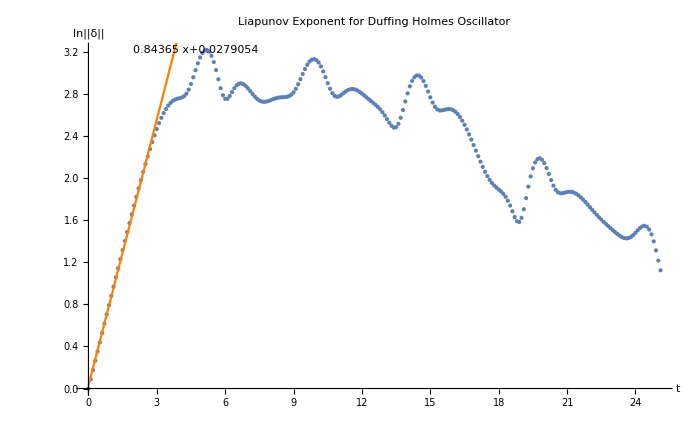

```mathematica
liap[0.1,8π,0,0,0.01,0.01,0.1,1,0.25]
```